# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Fe-Ni 5000Z Hysteresekurve.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

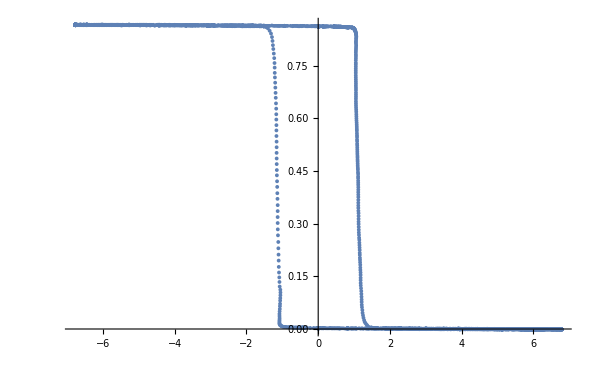

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=610;
d=(da+di)/2;
R=67.8;
```

```mathematica
N2=56;
A=h (da-di)/2;
messbereich=100;
fullfaktor=0.9;
```

```mathematica
dataProcessed={-N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

-0.0417645

1.43188

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

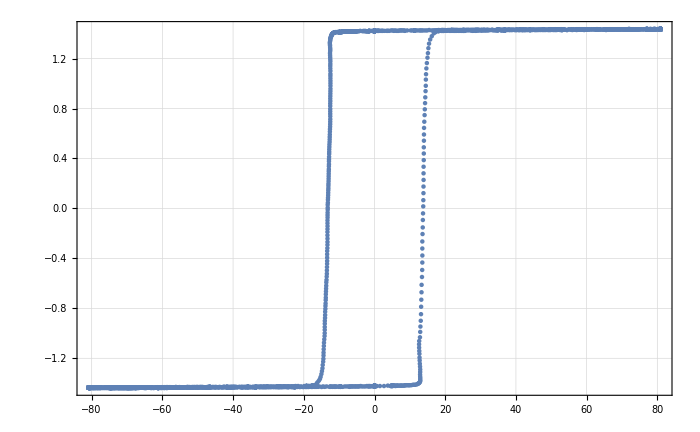

```mathematica
ListPlot[dataShifted,pltsettings]
```

## Remanence & Coercivity

```mathematica
sortedx=SortBy[dataShifted,Abs[Last[#]]&];
```

```mathematica
reg1data=DeleteCases[sortedx,x_/;x[[1]]<0][[1;;10]];
fit1=LinearModelFit[reg1data,x,x];
pars1=ungewichteterReg[reg1data[[All,1]],reg1data[[All,2]]];
reg2data=DeleteCases[sortedx,x_/;x[[1]]>0][[1;;10]];
fit2=LinearModelFit[reg2data,x,x];
pars2=ungewichteterReg[reg2data[[All,1]],reg2data[[All,2]]];
```

```mathematica
sortedy=SortBy[dataShifted,Abs[First[#]]&];
```

```mathematica
reg3data=DeleteCases[sortedy,x_/;x[[2]]<0][[1;;100]];
fit3=LinearModelFit[reg3data,x,x];
pars3=ungewichteterReg[reg3data[[All,1]],reg3data[[All,2]]];
reg4data=DeleteCases[sortedy,x_/;x[[2]]>0][[1;;100]];
fit4=LinearModelFit[reg4data,x,x];
pars4=ungewichteterReg[reg4data[[All,1]],reg4data[[All,2]]];
```

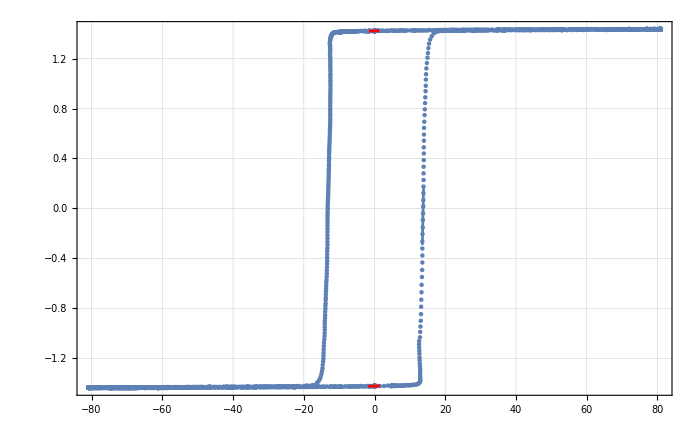

```mathematica
Show[ListPlot[dataShifted],Plot[fit1[x],{x,Min[reg1data[[All,1]]],Max[reg1data[[All,1]]]}],Plot[fit2[x],{x,Min[reg2data[[All,1]]],Max[reg2data[[All,1]]]}],Plot[fit3[x],{x,Min[reg3data[[All,1]]],Max[reg3data[[All,1]]]},PlotStyle->Red],Plot[fit4[x],{x,Min[reg4data[[All,1]]],Max[reg4data[[All,1]]]},PlotStyle->Red],pltsettings]
```

```mathematica
pltHeights=0.4;
```

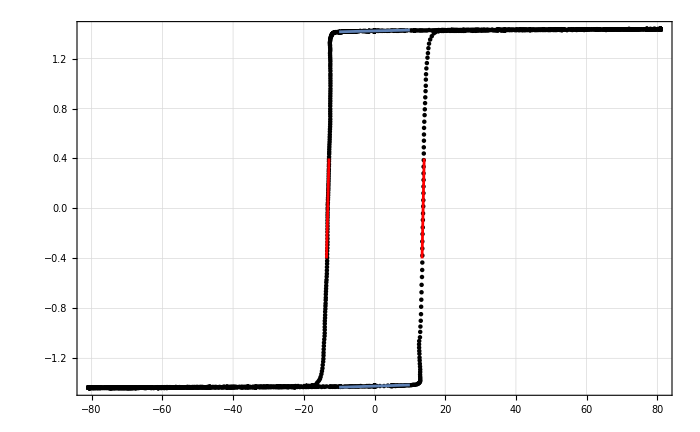

```mathematica
Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-10,10}],Plot[fit4[x],{x,-10,10}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/ni-fe 5000Z raw.pdf",Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-10,10}],Plot[fit4[x],{x,-10,10}],pltsettings],Background->None];
```

## Remance and coercitivity

```mathematica
Brp=pars3[[1]]
dBrp=pars3[[3]]
Brm=pars4[[1]]
dBrm=pars3[[3]]
```

1.42137

0.000123946

-1.42263

0.000123946

```mathematica
NumberForm[(Brp/dBrp^2 +Abs@Brm/dBrm^2)/(1/dBrp^2 + 1/dBrm^2),10]
```

1.421997743

```mathematica
1/Sqrt[(1/dBrp^2 + 1/dBrm^2)]
```

0.0000876433

```mathematica
Hm=pars2[[1]]/pars2[[2]]
```

13.2311

```mathematica
dHm=Abs[pars2[[1]]/pars2[[2]]]Sqrt[(pars2[[3]]/pars2[[1]])^2 +(pars2[[4]]/pars2[[2]])^2 ]
```

2.00673

```mathematica
Hp=pars1[[1]]/pars1[[2]]
```

-13.7467

```mathematica
dHp=Abs[pars1[[1]]/pars1[[2]]]Sqrt[(pars1[[3]]/pars1[[1]])^2 +(pars1[[4]]/pars1[[2]])^2 ]
```

1.11595

```mathematica
(Abs@Hp/dHp^2 +Hm/dHm^2)/(1/dHp^2 + 1/dHm^2)
```

13.6249

```mathematica
Sqrt[1/(1/dHp^2 + 1/dHm^2)]
```

0.975292